## Introduction

Analysis for paper XXX

## Analysis in (sum, diff) coordinates E = 0

### Define equations

```mathematica
Clear[b,j,k]
es={
2e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
2e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.e->0/.b->1;
TableForm[es]
```

-Cos[xp] Sin[xm]
-1/2 j Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

### Bifurcations

#### Saddle node

```mathematica
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
temp=Flatten[{es,Det[J]}];
sn=Solve[temp==0];
Length[sn]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -ArcCos[Cos[θp]] == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -ArcCos[Cos[θm]] == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -ArcCos[Cos[xp]] == 0.

General::stop: Further output of Solve::incnst will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

72

```mathematica
DeleteDuplicates[{j,k}/.sn]//TableForm
```

-1 | k
1 | k
j | -1
j | 1

Ok. So there are some saddle nodes at ±1

#### Hopf

```mathematica
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
temp=Flatten[{es,Tr[J]}];
hopf=Solve[temp==0];
Length[hopf]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

49

```mathematica
hopf[[1;;5]]//TableForm
```

j→-2-k | xm→-π/2 | xp→-π/2 | θm→0 | θp→0
j→-2-k | xm→-π/2 | xp→-π/2 | θm→-π | θp→0
j→-2-k | xm→-π/2 | xp→-π/2 | θm→π | θp→0
j→-2-k | xm→π/2 | xp→π/2 | θm→0 | θp→0
j→-2-k | xm→π/2 | xp→π/2 | θm→-π | θp→0

```mathematica
DeleteDuplicates[{j,k}/.hopf]//TableForm
```

-2-k | k
2-k | k
j | -4-j
j | -2-j
j | 2-j
j | 4-j
j | -j

So here are the hopf

#### Takens bogdanov

```mathematica
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
temp=Flatten[{es,Det[J],Tr[J]}];
tb=Solve[temp==0];
Length[tb]
```

120

```mathematica
DeleteDuplicates[{j,k}/.tb]//TableForm
```

-3 | -1
-1 | -3
-1 | -1
-1 | 1
1 | -1
1 | 1
1 | 3
3 | 1
-3 √(3/2) | 3 √(3/2)
3 √(3/2) | -3 √(3/2)
-ⅈ/(√2) | ⅈ/(√2)
ⅈ/(√2) | -ⅈ/(√2)

Interesting. So there’s a bunch of TB points here!

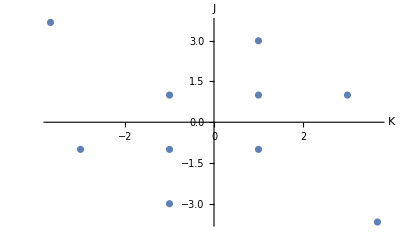

```mathematica
ListPlot[DeleteDuplicates[{j,k}/.tb],AxesLabel->{Style["K",Italic],Style["J",Italic]},LabelStyle->15]
```

#### Plot

I’ll plot the SN and hopf curves by hand, and the TB points automatically.

```mathematica
DeleteDuplicates[{j,k}/.hopf]//TableForm
```

-2-k | k
2-k | k
j | -4-j
j | -2-j
j | 2-j
j | 4-j
j | -j

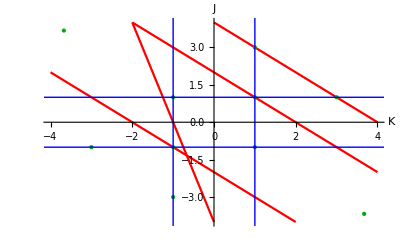

figures/bif-diagram-E-zero.png

```mathematica
p1=Plot[{-2-k,2-k,-4-4k,4-k},{k,-4,4},AxesLabel->{Style["K",Italic],Style["J",Italic]},LabelStyle->20,PlotRange->{-4,4},PlotStyle->{Red},
Epilog->{
Blue,
Line[{{-1,-10},{-1,10}}],
Line[{{1,-10},{1,10}}],
Line[{{-10,1},{10,1}}],
Line[{{-10,-1},{10,-1}}]
}
];
pTB=ListPlot[DeleteDuplicates[{j,k}/.tb],AxesLabel->{Style["K",Italic],Style["J",Italic]},ImageSize->Medium,LabelStyle->20,PlotStyle->{PointSize[Large],Darker[Green]}];
pFinal = Show[{p1,pTB}]
SetDirectory[NotebookDirectory[]];
Export["figures/bif-diagram-E-zero.png",pFinal]
```

1. Blue are saddle nodes
2. Red are hopf’s
3. Green are TB ponts

### Solve for fp

```mathematica
Clear[b,k]
fp=Solve[(es/.b->0.5)=={0,0,0,0},{xp,xm,θp,θm}];
TableForm[fp]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1
 |  |  |  |

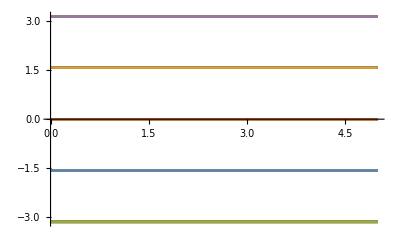

```mathematica
Plot[xp/.fp/.{C[1]->0,C[2]->0,C[3]->0,b->0.5,k->k1}//Evaluate,{k1,0,5}]
```

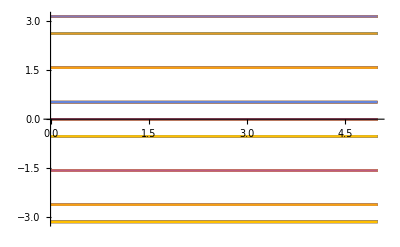

```mathematica
Plot[xm/.fp/.{C[1]->0,C[2]->0,C[3]->0,b->0.5,k->k1}//Evaluate,{k1,0,5}]
```

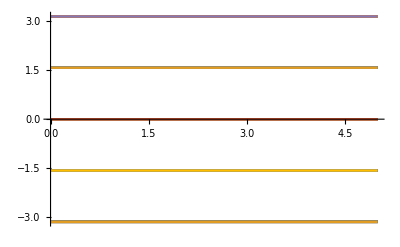

```mathematica
Plot[θp/.fp/.{C[1]->0,C[2]->0,C[3]->0,b->0.5,k->k1}//Evaluate,{k1,0,5}]
```

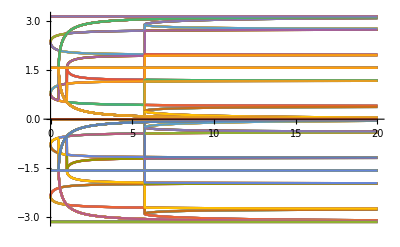

```mathematica
Plot[θm/.fp/.{C[1]->0,C[2]->0,C[3]->0,b->0.5,k->k1}//Evaluate,{k1,0,20}]
```

Interesting. Do we see this?

## Analysis in (sum, diff) coordinates E > 0 and J = K

### Define equations

```mathematica
Clear[b,j,k]
es={
2e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
2e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.b->1/.j->k;
TableForm[es]
```

2 e-Cos[xp] Sin[xm]
-1/2 k Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
2 e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]

### Bifurcations

#### Saddle node

```mathematica
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
det=FullSimplify[Det[J]];
temp=Flatten[{es,det}];
sn=Solve[temp==0];
Length[sn]
```

$Aborted

0

```mathematica
DeleteDuplicates[{k,e}/.sn]//TableForm
```

-1 | k
1 | k
j | -1
j | 1

#### Hopf

```mathematica
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
temp=Flatten[{es,Tr[J]}];
hopf=Solve[temp==0];
Length[hopf]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

258

```mathematica
cleanHopf=DeleteDuplicates[{k,e}/.hopf]//FullSimplify;
TableForm[cleanHopf]
```

0 | -1/2 √(Sin[xm]^2)
0 | 1/2 √(Sin[xm]^2)
-(Cos[xm] √(-1+2 Cos[xm]^2-Cos[xm]^6))/(√(-1+Cos[xm]^2+Cos[xm]^4) √Cos[2 xm] √(Sin[xm]^2)) | -(√(-1+Cos[xm]^2+Cos[xm]^4) √(Sin[xm]^2))/(2 √Cos[2 xm])
(Cos[xm] √(-1+2 Cos[xm]^2-Cos[xm]^6))/(√(-1+Cos[xm]^2+Cos[xm]^4) √Cos[2 xm] √(Sin[xm]^2)) | -(√(-1+Cos[xm]^2+Cos[xm]^4) √(Sin[xm]^2))/(2 √Cos[2 xm])
-(Cos[xm] √(-1+2 Cos[xm]^2-Cos[xm]^6))/(√(-1+Cos[xm]^2+Cos[xm]^4) √Cos[2 xm] √(Sin[xm]^2)) | (√(-1+Cos[xm]^2+Cos[xm]^4) √(Sin[xm]^2))/(2 √Cos[2 xm])
(Cos[xm] √(-1+2 Cos[xm]^2-Cos[xm]^6))/(√(-1+Cos[xm]^2+Cos[xm]^4) √Cos[2 xm] √(Sin[xm]^2)) | (√(-1+Cos[xm]^2+Cos[xm]^4) √(Sin[xm]^2))/(2 √Cos[2 xm])
-(√(Sin[2 θm]^2))/(2 √Cos[2 θm] √(Sin[θm]^2)) | -(√(-1+Cos[θm]^2+Cos[θm]^4) √(Sin[θm]^2))/(2 √Cos[2 θm])
(√(Sin[2 θm]^2))/(2 √Cos[2 θm] √(Sin[θm]^2)) | -(√(-1+Cos[θm]^2+Cos[θm]^4) √(Sin[θm]^2))/(2 √Cos[2 θm])
-(√(Sin[2 θm]^2))/(2 √Cos[2 θm] √(Sin[θm]^2)) | (√(-1+Cos[θm]^2+Cos[θm]^4) √(Sin[θm]^2))/(2 √Cos[2 θm])
(√(Sin[2 θm]^2))/(2 √Cos[2 θm] √(Sin[θm]^2)) | (√(-1+Cos[θm]^2+Cos[θm]^4) √(Sin[θm]^2))/(2 √Cos[2 θm])
0 | -Cos[θp]/2
-2 √(Sin[θp]^2) | -Cos[θp]/2
2 √(Sin[θp]^2) | -Cos[θp]/2
0 | Cos[θp]/2
-2 √(Sin[θp]^2) | Cos[θp]/2
2 √(Sin[θp]^2) | Cos[θp]/2

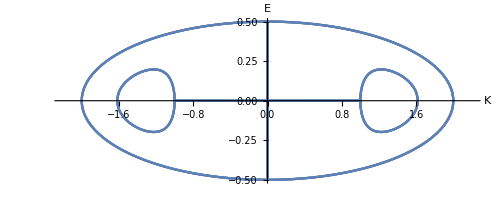

```mathematica
p1=ParametricPlot[cleanHopf[[1;;6]],{xm,-π,π},AxesLabel->{Style["K",18,Italic],Style["E",18,Italic]},LabelStyle->15,PlotRange->{{-2.2,2.2},Automatic}];
p2=ParametricPlot[cleanHopf[[6;;10]],{θm,-π,π},AxesLabel->{"K","E"},LabelStyle->15];
p3=ParametricPlot[cleanHopf[[11;;-1]],{θp,-π,π},AxesLabel->{"K","E"},LabelStyle->15];
p4=Show[{p1,p3}]
```

Nice!

```mathematica
cleanHopf/.{xp->SubPlus[x],xm->SubMinus[x],θp->SubPlus[θ],θm->SubMinus[θ]}//TableForm//TeXForm
```

\begin{array}{cc}
 0 & -\frac{1}{2} \sqrt{\sin ^2\left(x_-\right)} \\
 0 & \frac{1}{2} \sqrt{\sin ^2\left(x_-\right)} \\
 -\frac{\cos \left(x_-\right) \sqrt{-\cos ^6\left(x_-\right)+2 \cos ^2\left(x_-\right)-1}}{\sqrt{\sin ^2\left(x_-\right)} \sqrt{\cos ^4\left(x_-\right)+\cos ^2\left(x_-\right)-1} \sqrt{\cos \left(2
   x_-\right)}} & -\frac{\sqrt{\sin ^2\left(x_-\right)} \sqrt{\cos ^4\left(x_-\right)+\cos ^2\left(x_-\right)-1}}{2 \sqrt{\cos \left(2 x_-\right)}} \\
 \frac{\cos \left(x_-\right) \sqrt{-\cos ^6\left(x_-\right)+2 \cos ^2\left(x_-\right)-1}}{\sqrt{\sin ^2\left(x_-\right)} \sqrt{\cos ^4\left(x_-\right)+\cos ^2\left(x_-\right)-1} \sqrt{\cos \left(2
   x_-\right)}} & -\frac{\sqrt{\sin ^2\left(x_-\right)} \sqrt{\cos ^4\left(x_-\right)+\cos ^2\left(x_-\right)-1}}{2 \sqrt{\cos \left(2 x_-\right)}} \\
 -\frac{\cos \left(x_-\right) \sqrt{-\cos ^6\left(x_-\right)+2 \cos ^2\left(x_-\right)-1}}{\sqrt{\sin ^2\left(x_-\right)} \sqrt{\cos ^4\left(x_-\right)+\cos ^2\left(x_-\right)-1} \sqrt{\cos \left(2
   x_-\right)}} & \frac{\sqrt{\sin ^2\left(x_-\right)} \sqrt{\cos ^4\left(x_-\right)+\cos ^2\left(x_-\right)-1}}{2 \sqrt{\cos \left(2 x_-\right)}} \\
 \frac{\cos \left(x_-\right) \sqrt{-\cos ^6\left(x_-\right)+2 \cos ^2\left(x_-\right)-1}}{\sqrt{\sin ^2\left(x_-\right)} \sqrt{\cos ^4\left(x_-\right)+\cos ^2\left(x_-\right)-1} \sqrt{\cos \left(2
   x_-\right)}} & \frac{\sqrt{\sin ^2\left(x_-\right)} \sqrt{\cos ^4\left(x_-\right)+\cos ^2\left(x_-\right)-1}}{2 \sqrt{\cos \left(2 x_-\right)}} \\
 -\frac{\sqrt{\sin ^2\left(2 \theta _-\right)}}{2 \sqrt{\sin ^2\left(\theta _-\right)} \sqrt{\cos \left(2 \theta _-\right)}} & -\frac{\sqrt{\sin ^2\left(\theta _-\right)} \sqrt{\cos ^4\left(\theta
   _-\right)+\cos ^2\left(\theta _-\right)-1}}{2 \sqrt{\cos \left(2 \theta _-\right)}} \\
 \frac{\sqrt{\sin ^2\left(2 \theta _-\right)}}{2 \sqrt{\sin ^2\left(\theta _-\right)} \sqrt{\cos \left(2 \theta _-\right)}} & -\frac{\sqrt{\sin ^2\left(\theta _-\right)} \sqrt{\cos ^4\left(\theta
   _-\right)+\cos ^2\left(\theta _-\right)-1}}{2 \sqrt{\cos \left(2 \theta _-\right)}} \\
 -\frac{\sqrt{\sin ^2\left(2 \theta _-\right)}}{2 \sqrt{\sin ^2\left(\theta _-\right)} \sqrt{\cos \left(2 \theta _-\right)}} & \frac{\sqrt{\sin ^2\left(\theta _-\right)} \sqrt{\cos ^4\left(\theta
   _-\right)+\cos ^2\left(\theta _-\right)-1}}{2 \sqrt{\cos \left(2 \theta _-\right)}} \\
 \frac{\sqrt{\sin ^2\left(2 \theta _-\right)}}{2 \sqrt{\sin ^2\left(\theta _-\right)} \sqrt{\cos \left(2 \theta _-\right)}} & \frac{\sqrt{\sin ^2\left(\theta _-\right)} \sqrt{\cos ^4\left(\theta
   _-\right)+\cos ^2\left(\theta _-\right)-1}}{2 \sqrt{\cos \left(2 \theta _-\right)}} \\
 0 & -\frac{1}{2} \cos \left(\theta _+\right) \\
 -2 \sqrt{\sin ^2\left(\theta _+\right)} & -\frac{1}{2} \cos \left(\theta _+\right) \\
 2 \sqrt{\sin ^2\left(\theta _+\right)} & -\frac{1}{2} \cos \left(\theta _+\right) \\
 0 & \frac{\cos \left(\theta _+\right)}{2} \\
 -2 \sqrt{\sin ^2\left(\theta _+\right)} & \frac{\cos \left(\theta _+\right)}{2} \\
 2 \sqrt{\sin ^2\left(\theta _+\right)} & \frac{\cos \left(\theta _+\right)}{2} \\
\end{array}

#### Takens bogdanov

```mathematica
J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
temp=Flatten[{es,Det[J],Tr[J]}];
tb=Solve[temp==0];
Length[tb]
```

296

Let’s plot them along with the Hopf curves

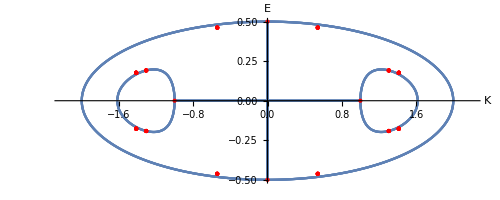

figures/bif-diagram-E-nonzero.png

```mathematica
p5=ListPlot[DeleteDuplicates[{k,e}/.tb],AxesLabel->{Style["K",Italic],Style["E",Italic]},LabelStyle->15,PlotStyle->{Red,PointSize[Large]}];
pFinal1 = Show[p4,p5]
SetDirectory[NotebookDirectory[]];
Export["figures/bif-diagram-E-nonzero.png",pFinal1]
```

That’s beautiful! I hope its genuine.

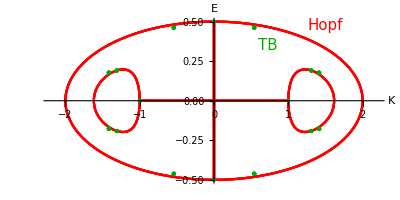

figures/bif-diagram-E-nonzero.png

```mathematica
(*Colors*)
colorSN=Blue;
colorHopf=Red;
colorTB=Darker[Green];

(*Hopf plots*)
p1=ParametricPlot[cleanHopf[[1;;6]],{xm,-π,π},
AxesLabel->{Style["K",18,Italic],Style["E",18,Italic]},
LabelStyle->15,
PlotRange->{{-2.2,2.2},Automatic},
PlotStyle->colorHopf,
AspectRatio->1/2,
Epilog->{Text[Style["Hopf",15,colorHopf],{1.5,0.475}], Text[Style["TB",15,colorTB],{0.72,0.35}]}
];
p2=ParametricPlot[cleanHopf[[6;;10]],{θm,-π,π},AxesLabel->{"K","E"},LabelStyle->15,PlotStyle->colorHopf];
p3=ParametricPlot[cleanHopf[[11;;-1]],{θp,-π,π},AxesLabel->{"K","E"},LabelStyle->15,PlotStyle->colorHopf];
p4=Show[{p1,p2,p3}];

(*TB*)
p5=ListPlot[DeleteDuplicates[{k,e}/.tb],AxesLabel->{Style["K",Italic],Style["E",Italic]},LabelStyle->15,PlotStyle->{colorTB,PointSize[Large]}];
pFinal1 = Show[p4,p5]
SetDirectory[NotebookDirectory[]];
Export["figures/bif-diagram-E-nonzero.png",pFinal1]
```

```mathematica
DeleteDuplicates[{k,e}/.tb]//TableForm
```

0 | -1/2
-1 | 0
1 | 0
0 | 1/2
Root-0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{1,1}]-0.541196100146197 | Root-0.462Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,-#2+2 #3&},{1,1,1}]-0.46193976625564337
Root0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{1,2}]0.541196100146197 | Root-0.462Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,-#2+2 #3&},{1,1,1}]-0.46193976625564337
Root-0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{1,1}]-0.541196100146197 | Root0.462Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,-#2+2 #3&},{1,2,1}]0.46193976625564337
Root0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{1,2}]0.541196100146197 | Root0.462Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,-#2+2 #3&},{1,2,1}]0.46193976625564337
Root-1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{2,1}]-1.3065629648763766 | Root-0.191Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,-#2+2 #3&},{2,1,1}]-0.1913417161825449
Root1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{2,2}]1.3065629648763766 | Root-0.191Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,-#2+2 #3&},{2,1,1}]-0.1913417161825449
Root-1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{2,1}]-1.3065629648763766 | Root0.191Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,-#2+2 #3&},{2,2,1}]0.1913417161825449
Root1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{2,2}]1.3065629648763766 | Root0.191Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,-#2+2 #3&},{2,2,1}]0.1913417161825449
Root-1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{3,1}]-1.3065629648763766 | Root-0.191Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,-#2+2 #3&},{3,1,1}]-0.1913417161825449
Root1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{3,2}]1.3065629648763766 | Root-0.191Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,-#2+2 #3&},{3,1,1}]-0.1913417161825449
Root-1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{3,1}]-1.3065629648763766 | Root0.191Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,-#2+2 #3&},{3,2,1}]0.1913417161825449
Root1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{3,2}]1.3065629648763766 | Root0.191Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,-#2+2 #3&},{3,2,1}]0.1913417161825449
Root-0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{4,1}]-0.541196100146197 | Root-0.462Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,-#2+2 #3&},{4,1,1}]-0.46193976625564337
Root0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{4,2}]0.541196100146197 | Root-0.462Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,-#2+2 #3&},{4,1,1}]-0.46193976625564337
Root-0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{4,1}]-0.541196100146197 | Root0.462Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,-#2+2 #3&},{4,2,1}]0.46193976625564337
Root0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{4,2}]0.541196100146197 | Root0.462Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,-#2+2 #3&},{4,2,1}]0.46193976625564337
Root-0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{1,1}]-0.541196100146197 | Root0.462Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,#2+2 #3&},{1,1,1}]0.46193976625564337
Root0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{1,2}]0.541196100146197 | Root0.462Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,#2+2 #3&},{1,1,1}]0.46193976625564337
Root-0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{1,1}]-0.541196100146197 | Root-0.462Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,#2+2 #3&},{1,2,1}]-0.46193976625564337
Root0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{1,2}]0.541196100146197 | Root-0.462Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,#2+2 #3&},{1,2,1}]-0.46193976625564337
Root-1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{2,1}]-1.3065629648763766 | Root0.191Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,#2+2 #3&},{2,1,1}]0.1913417161825449
Root1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{2,2}]1.3065629648763766 | Root0.191Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,#2+2 #3&},{2,1,1}]0.1913417161825449
Root-1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{2,1}]-1.3065629648763766 | Root-0.191Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,#2+2 #3&},{2,2,1}]-0.1913417161825449
Root1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{2,2}]1.3065629648763766 | Root-0.191Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,#2+2 #3&},{2,2,1}]-0.1913417161825449
Root-1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{3,1}]-1.3065629648763766 | Root0.191Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,#2+2 #3&},{3,1,1}]0.1913417161825449
Root1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{3,2}]1.3065629648763766 | Root0.191Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,#2+2 #3&},{3,1,1}]0.1913417161825449
Root-1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{3,1}]-1.3065629648763766 | Root-0.191Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,#2+2 #3&},{3,2,1}]-0.1913417161825449
Root1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{3,2}]1.3065629648763766 | Root-0.191Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,#2+2 #3&},{3,2,1}]-0.1913417161825449
Root-0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{4,1}]-0.541196100146197 | Root0.462Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,#2+2 #3&},{4,1,1}]0.46193976625564337
Root0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{4,2}]0.541196100146197 | Root0.462Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,#2+2 #3&},{4,1,1}]0.46193976625564337
Root-0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{4,1}]-0.541196100146197 | Root-0.462Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,#2+2 #3&},{4,2,1}]-0.46193976625564337
Root0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{4,2}]0.541196100146197 | Root-0.462Root[{1-4 #1^2+2 #1^4&,3 #1^2-19 #1^4+29 #1^6-18 #1^8+4 #1^10+#2^2&,#2+2 #3&},{4,2,1}]-0.46193976625564337
Root-0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{1,1}]-0.541196100146197 | Root0.462Root[{1-4 #1^2+2 #1^4&,-1+9 #1^2-39 #1^4+58 #1^6-36 #1^8+8 #1^10+#2^2&,-#1 #2+2 #3&},{1,1,1}]0.46193976625564337
Root0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{1,2}]0.541196100146197 | Root0.462Root[{1-4 #1^2+2 #1^4&,-1+9 #1^2-39 #1^4+58 #1^6-36 #1^8+8 #1^10+#2^2&,-#1 #2+2 #3&},{1,1,1}]0.46193976625564337
Root-0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{1,1}]-0.541196100146197 | Root-0.462Root[{1-4 #1^2+2 #1^4&,-1+9 #1^2-39 #1^4+58 #1^6-36 #1^8+8 #1^10+#2^2&,-#1 #2+2 #3&},{1,2,1}]-0.46193976625564337
Root0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{1,2}]0.541196100146197 | Root-0.462Root[{1-4 #1^2+2 #1^4&,-1+9 #1^2-39 #1^4+58 #1^6-36 #1^8+8 #1^10+#2^2&,-#1 #2+2 #3&},{1,2,1}]-0.46193976625564337
Root-1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{2,1}]-1.3065629648763766 | Root0.191Root[{1-4 #1^2+2 #1^4&,-1+9 #1^2-39 #1^4+58 #1^6-36 #1^8+8 #1^10+#2^2&,-#1 #2+2 #3&},{2,1,1}]0.1913417161825449
Root1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{2,2}]1.3065629648763766 | Root0.191Root[{1-4 #1^2+2 #1^4&,-1+9 #1^2-39 #1^4+58 #1^6-36 #1^8+8 #1^10+#2^2&,-#1 #2+2 #3&},{2,1,1}]0.1913417161825449
Root-1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{2,1}]-1.3065629648763766 | Root-0.191Root[{1-4 #1^2+2 #1^4&,-1+9 #1^2-39 #1^4+58 #1^6-36 #1^8+8 #1^10+#2^2&,-#1 #2+2 #3&},{2,2,1}]-0.1913417161825449
Root1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{2,2}]1.3065629648763766 | Root-0.191Root[{1-4 #1^2+2 #1^4&,-1+9 #1^2-39 #1^4+58 #1^6-36 #1^8+8 #1^10+#2^2&,-#1 #2+2 #3&},{2,2,1}]-0.1913417161825449
Root-1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{3,1}]-1.3065629648763766 | Root-0.191Root[{1-4 #1^2+2 #1^4&,-1+9 #1^2-39 #1^4+58 #1^6-36 #1^8+8 #1^10+#2^2&,-#1 #2+2 #3&},{3,1,1}]-0.1913417161825449
Root1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{3,2}]1.3065629648763766 | Root-0.191Root[{1-4 #1^2+2 #1^4&,-1+9 #1^2-39 #1^4+58 #1^6-36 #1^8+8 #1^10+#2^2&,-#1 #2+2 #3&},{3,1,1}]-0.1913417161825449
Root-1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{3,1}]-1.3065629648763766 | Root0.191Root[{1-4 #1^2+2 #1^4&,-1+9 #1^2-39 #1^4+58 #1^6-36 #1^8+8 #1^10+#2^2&,-#1 #2+2 #3&},{3,2,1}]0.1913417161825449
Root1.31Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{3,2}]1.3065629648763766 | Root0.191Root[{1-4 #1^2+2 #1^4&,-1+9 #1^2-39 #1^4+58 #1^6-36 #1^8+8 #1^10+#2^2&,-#1 #2+2 #3&},{3,2,1}]0.1913417161825449
Root-0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{4,1}]-0.541196100146197 | Root-0.462Root[{1-4 #1^2+2 #1^4&,-1+9 #1^2-39 #1^4+58 #1^6-36 #1^8+8 #1^10+#2^2&,-#1 #2+2 #3&},{4,1,1}]-0.46193976625564337
Root0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{4,2}]0.541196100146197 | Root-0.462Root[{1-4 #1^2+2 #1^4&,-1+9 #1^2-39 #1^4+58 #1^6-36 #1^8+8 #1^10+#2^2&,-#1 #2+2 #3&},{4,1,1}]-0.46193976625564337
Root-0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{4,1}]-0.541196100146197 | Root0.462Root[{1-4 #1^2+2 #1^4&,-1+9 #1^2-39 #1^4+58 #1^6-36 #1^8+8 #1^10+#2^2&,-#1 #2+2 #3&},{4,2,1}]0.46193976625564337
Root0.541Root[{1-4 #1^2+2 #1^4&,-1-17 #1^2+78 #1^4-116 #1^6+72 #1^8-16 #1^10+#2^2&},{4,2}]0.541196100146197 | Root0.462Root[{1-4 #1^2+2 #1^4&,-1+9 #1^2-39 #1^4+58 #1^6-36 #1^8+8 #1^10+#2^2&,-#1 #2+2 #3&},{4,2,1}]0.46193976625564337
Root-1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{1,1,1}]-1.4142135623730951 | Root0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{1,1,1,1}]0.1767766952966369
Root1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{1,1,2}]1.4142135623730951 | Root0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{1,1,1,1}]0.1767766952966369
Root-1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{1,1,1}]-1.4142135623730951 | Root-0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{1,1,2,1}]-0.1767766952966369
Root1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{1,1,2}]1.4142135623730951 | Root-0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{1,1,2,1}]-0.1767766952966369
Root-1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{1,2,1}]-1.4142135623730951 | Root-0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{1,2,1,1}]-0.1767766952966369
Root1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{1,2,2}]1.4142135623730951 | Root-0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{1,2,1,1}]-0.1767766952966369
Root-1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{1,2,1}]-1.4142135623730951 | Root0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{1,2,2,1}]0.1767766952966369
Root1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{1,2,2}]1.4142135623730951 | Root0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{1,2,2,1}]0.1767766952966369
Root-1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{2,1,1}]-1.4142135623730951 | Root0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{2,1,1,1}]0.1767766952966369
Root1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{2,1,2}]1.4142135623730951 | Root0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{2,1,1,1}]0.1767766952966369
Root-1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{2,1,1}]-1.4142135623730951 | Root-0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{2,1,2,1}]-0.1767766952966369
Root1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{2,1,2}]1.4142135623730951 | Root-0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{2,1,2,1}]-0.1767766952966369
Root-1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{2,2,1}]-1.4142135623730951 | Root-0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{2,2,1,1}]-0.1767766952966369
Root1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{2,2,2}]1.4142135623730951 | Root-0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{2,2,1,1}]-0.1767766952966369
Root-1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{2,2,1}]-1.4142135623730951 | Root0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{2,2,2,1}]0.1767766952966369
Root1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{2,2,2}]1.4142135623730951 | Root0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{2,2,2,1}]0.1767766952966369
Root-1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{3,1,1}]-1.4142135623730951 | Root0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{3,1,1,1}]0.1767766952966369
Root1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{3,1,2}]1.4142135623730951 | Root0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{3,1,1,1}]0.1767766952966369
Root-1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{3,1,1}]-1.4142135623730951 | Root-0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{3,1,2,1}]-0.1767766952966369
Root1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{3,1,2}]1.4142135623730951 | Root-0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{3,1,2,1}]-0.1767766952966369
Root-1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{3,2,1}]-1.4142135623730951 | Root-0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{3,2,1,1}]-0.1767766952966369
Root1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{3,2,2}]1.4142135623730951 | Root-0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{3,2,1,1}]-0.1767766952966369
Root-1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{3,2,1}]-1.4142135623730951 | Root0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{3,2,2,1}]0.1767766952966369
Root1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{3,2,2}]1.4142135623730951 | Root0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{3,2,2,1}]0.1767766952966369
Root-1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{4,1,1}]-1.4142135623730951 | Root0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{4,1,1,1}]0.1767766952966369
Root1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{4,1,2}]1.4142135623730951 | Root0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{4,1,1,1}]0.1767766952966369
Root-1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{4,1,1}]-1.4142135623730951 | Root-0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{4,1,2,1}]-0.1767766952966369
Root1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{4,1,2}]1.4142135623730951 | Root-0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{4,1,2,1}]-0.1767766952966369
Root-1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{4,2,1}]-1.4142135623730951 | Root-0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{4,2,1,1}]-0.1767766952966369
Root1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{4,2,2}]1.4142135623730951 | Root-0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{4,2,1,1}]-0.1767766952966369
Root-1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{4,2,1}]-1.4142135623730951 | Root0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{4,2,2,1}]0.1767766952966369
Root1.41Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2+3 #1^2-82 #1^4+160 #1^6-80 #1^8+#2^2+#3^2&},{4,2,2}]1.4142135623730951 | Root0.177Root[{1-8 #1^2+8 #1^4&,1-#1^2-8 #1^4+16 #1^6-8 #1^8-#2^2+#1^2 #2^2&,-2 #1^2+9 #1^4-16 #1^6+8 #1^8+#3^2&,-#2 #3+2 #4&},{4,2,2,1}]0.1767766952966369

### Fixed points

#### Warm up: E = 0

```mathematica
Clear[b,k]
fp=Solve[(es/.e->0)=={0,0,0,0},{xp,xm,θp,θm}];
Length[fp]
TableForm[fp]
```

208

1
 |  |  |  |

```mathematica
fp[[1;;5]]//TableForm
```

xp→ConditionalExpression[2 π C[2], C[2]∈ℤ] | xm→ConditionalExpression[2 π C[1], C[1]∈ℤ] | θp→ConditionalExpression[2 π C[4], C[4]∈ℤ] | θm→ConditionalExpression[2 π C[3], C[3]∈ℤ]
xp→ConditionalExpression[2 π C[2], C[2]∈ℤ] | xm→ConditionalExpression[2 π C[1], C[1]∈ℤ] | θp→ConditionalExpression[2 π C[4], C[4]∈ℤ] | θm→ConditionalExpression[π+2 π C[3], C[3]∈ℤ]
xp→ConditionalExpression[2 π C[2], C[2]∈ℤ] | xm→ConditionalExpression[2 π C[1], C[1]∈ℤ] | θp→ConditionalExpression[-π/2+2 π C[4], C[4]∈ℤ] | θm→ConditionalExpression[-π/2+2 π C[3], C[3]∈ℤ]
xp→ConditionalExpression[2 π C[2], C[2]∈ℤ] | xm→ConditionalExpression[2 π C[1], C[1]∈ℤ] | θp→ConditionalExpression[-π/2+2 π C[4], C[4]∈ℤ] | θm→ConditionalExpression[π/2+2 π C[3], C[3]∈ℤ]
xp→ConditionalExpression[2 π C[2], C[2]∈ℤ] | xm→ConditionalExpression[2 π C[1], C[1]∈ℤ] | θp→ConditionalExpression[-π/2+2 π C[4], C[4]∈ℤ] | θm→ConditionalExpression[ArcTan[-(√(-1+k^2))/k,1/k]+2 π C[3], C[3]∈ℤ]

```mathematica
fpClean=DeleteDuplicates[fp/.{C[1]->0,C[2]->0,C[3]->0,C[4]->0,C[5]->0}];
```

208

No simplifications

```mathematica
Plot[xp/.fp/.{C[1]->0,C[2]->0,C[3]->0,C[4]->0,C[5]->0,e->0,k->k1}//Evaluate,{k1,-5,5}]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

$Aborted

Hmm, still costly. This will take work.

#### Main: E > 0

```mathematica
Clear[b,k]
fp=Solve[(es)=={0,0,0,0},{xp,xm,θp,θm}];
Length[fp]
TableForm[fp]
```

$Aborted

208

$Aborted[]

## Co-dimension 3: (J,KE) space

#### Warm up

```mathematica
Clear[b,j,k]
es={
2e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
2e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.b->1/.j->k;
TableForm[es];

J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
det=Det[J]//FullSimplify;
tr=Tr[J]//FullSimplify;
temp=Flatten[{es,det,tr}];
tb=Solve[temp==0];
Length[tb]
```

296

#### Set J = n k for n = 1,2,3

```mathematica
Clear[b,j,k]
es={
2e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
2e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.b->1/.j->2k;
TableForm[es];

J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
det=Det[J]//FullSimplify;
tr=Tr[J]//FullSimplify;
temp=Flatten[{es,det,tr}];
tb2=Solve[temp==0];
Length[tb2]
```

520

```mathematica
Clear[b,j,k]
es={
2e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
2e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.b->1/.j->300k;
TableForm[es];

J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
det=Det[J]//FullSimplify;
tr=Tr[J]//FullSimplify;
temp=Flatten[{es,det,tr}];
tb3=Solve[temp==0];
Length[tb3]
```

552

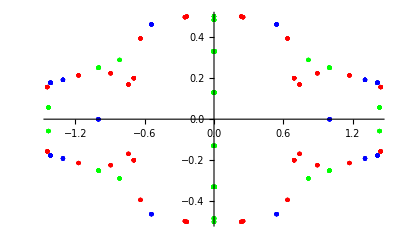

```mathematica
p1=ListPlot[{k,e}/.tb,PlotStyle->{Blue,PointSize[Large]}];
p2=ListPlot[{k,e}/.tb2,PlotStyle->{Red,PointSize[Large]}];
p3=ListPlot[{k,e}/.tb3,PlotStyle->{Green,PointSize[Large]}];
Show[{p1,p2,p3}]
```

```mathematica
{k,e}/.tb3//N//TableForm
```

0. | -0.5
0. | -0.5
0. | -0.5
0. | -0.5
-0.000270809 | -0.5
-0.000270809 | -0.5
-0.000270809 | -0.5
-0.000270809 | -0.5
-0.000270809 | -0.5
-0.000270809 | -0.5
-0.000270809 | -0.5
-0.000270809 | -0.5
0.000270809 | -0.5
0.000270809 | -0.5
0.000270809 | -0.5
0.000270809 | -0.5
0.000270809 | -0.5
0.000270809 | -0.5
0.000270809 | -0.5
0.000270809 | -0.5
0.-1.40716 ⅈ | -0.5
0.-1.40716 ⅈ | -0.5
0.-1.40716 ⅈ | -0.5
0.-1.40716 ⅈ | -0.5
0.-1.40716 ⅈ | -0.5
0.-1.40716 ⅈ | -0.5
0.-1.40716 ⅈ | -0.5
0.-1.40716 ⅈ | -0.5
0.+1.40716 ⅈ | -0.5
0.+1.40716 ⅈ | -0.5
0.+1.40716 ⅈ | -0.5
0.+1.40716 ⅈ | -0.5
0.+1.40716 ⅈ | -0.5
0.+1.40716 ⅈ | -0.5
0.+1.40716 ⅈ | -0.5
0.+1.40716 ⅈ | -0.5
0. | 0.5
0. | 0.5
0. | 0.5
0. | 0.5
-0.000270809 | 0.5
-0.000270809 | 0.5
-0.000270809 | 0.5
-0.000270809 | 0.5
-0.000270809 | 0.5
-0.000270809 | 0.5
-0.000270809 | 0.5
-0.000270809 | 0.5
0.000270809 | 0.5
0.000270809 | 0.5
0.000270809 | 0.5
0.000270809 | 0.5
0.000270809 | 0.5
0.000270809 | 0.5
0.000270809 | 0.5
0.000270809 | 0.5
0.-1.40716 ⅈ | 0.5
0.-1.40716 ⅈ | 0.5
0.-1.40716 ⅈ | 0.5
0.-1.40716 ⅈ | 0.5
0.-1.40716 ⅈ | 0.5
0.-1.40716 ⅈ | 0.5
0.-1.40716 ⅈ | 0.5
0.-1.40716 ⅈ | 0.5
0.+1.40716 ⅈ | 0.5
0.+1.40716 ⅈ | 0.5
0.+1.40716 ⅈ | 0.5
0.+1.40716 ⅈ | 0.5
0.+1.40716 ⅈ | 0.5
0.+1.40716 ⅈ | 0.5
0.+1.40716 ⅈ | 0.5
0.+1.40716 ⅈ | 0.5
-0.816951 | -0.288354
-0.816951 | -0.288354
-0.816951 | -0.288354
-0.816951 | -0.288354
-0.816951 | -0.288354
-0.816951 | -0.288354
-0.816951 | -0.288354
-0.816951 | -0.288354
0.816951 | -0.288354
0.816951 | -0.288354
0.816951 | -0.288354
0.816951 | -0.288354
0.816951 | -0.288354
0.816951 | -0.288354
0.816951 | -0.288354
0.816951 | -0.288354
-0.816951 | 0.288354
-0.816951 | 0.288354
-0.816951 | 0.288354
-0.816951 | 0.288354
-0.816951 | 0.288354
-0.816951 | 0.288354
-0.816951 | 0.288354
-0.816951 | 0.288354
0.816951 | 0.288354
0.816951 | 0.288354
0.816951 | 0.288354
0.816951 | 0.288354
0.816951 | 0.288354
0.816951 | 0.288354
0.816951 | 0.288354
0.816951 | 0.288354
0.-0.000273537 ⅈ | -0.501681
0.-0.000273537 ⅈ | -0.501681
0.-0.000273537 ⅈ | -0.501681
0.-0.000273537 ⅈ | -0.501681
0.-0.000273537 ⅈ | -0.501681
0.-0.000273537 ⅈ | -0.501681
0.-0.000273537 ⅈ | -0.501681
0.-0.000273537 ⅈ | -0.501681
0.-0.000273537 ⅈ | -0.501681
0.-0.000273537 ⅈ | -0.501681
0.-0.000273537 ⅈ | -0.501681
0.-0.000273537 ⅈ | -0.501681
0.-0.000273537 ⅈ | -0.501681
0.-0.000273537 ⅈ | -0.501681
0.-0.000273537 ⅈ | -0.501681
0.-0.000273537 ⅈ | -0.501681
0.+0.000273537 ⅈ | -0.501681
0.+0.000273537 ⅈ | -0.501681
0.+0.000273537 ⅈ | -0.501681
0.+0.000273537 ⅈ | -0.501681
0.+0.000273537 ⅈ | -0.501681
0.+0.000273537 ⅈ | -0.501681
0.+0.000273537 ⅈ | -0.501681
0.+0.000273537 ⅈ | -0.501681
0.+0.000273537 ⅈ | -0.501681
0.+0.000273537 ⅈ | -0.501681
0.+0.000273537 ⅈ | -0.501681
0.+0.000273537 ⅈ | -0.501681
0.+0.000273537 ⅈ | -0.501681
0.+0.000273537 ⅈ | -0.501681
0.+0.000273537 ⅈ | -0.501681
0.+0.000273537 ⅈ | -0.501681
0.-0.000273537 ⅈ | 0.501681
0.-0.000273537 ⅈ | 0.501681
0.-0.000273537 ⅈ | 0.501681
0.-0.000273537 ⅈ | 0.501681
0.-0.000273537 ⅈ | 0.501681
0.-0.000273537 ⅈ | 0.501681
0.-0.000273537 ⅈ | 0.501681
0.-0.000273537 ⅈ | 0.501681
0.-0.000273537 ⅈ | 0.501681
0.-0.000273537 ⅈ | 0.501681
0.-0.000273537 ⅈ | 0.501681
0.-0.000273537 ⅈ | 0.501681
0.-0.000273537 ⅈ | 0.501681
0.-0.000273537 ⅈ | 0.501681
0.-0.000273537 ⅈ | 0.501681
0.-0.000273537 ⅈ | 0.501681
0.+0.000273537 ⅈ | 0.501681
0.+0.000273537 ⅈ | 0.501681
0.+0.000273537 ⅈ | 0.501681
0.+0.000273537 ⅈ | 0.501681
0.+0.000273537 ⅈ | 0.501681
0.+0.000273537 ⅈ | 0.501681
0.+0.000273537 ⅈ | 0.501681
0.+0.000273537 ⅈ | 0.501681
0.+0.000273537 ⅈ | 0.501681
0.+0.000273537 ⅈ | 0.501681
0.+0.000273537 ⅈ | 0.501681
0.+0.000273537 ⅈ | 0.501681
0.+0.000273537 ⅈ | 0.501681
0.+0.000273537 ⅈ | 0.501681
0.+0.000273537 ⅈ | 0.501681
0.+0.000273537 ⅈ | 0.501681
-0.00172425 | -0.483302
-0.00172425 | -0.483302
0.00172425 | -0.483302
0.00172425 | -0.483302
-0.00172425 | 0.483302
-0.00172425 | 0.483302
0.00172425 | 0.483302
0.00172425 | 0.483302
-0.00642265 | -0.129749
-0.00642265 | -0.129749
0.00642265 | -0.129749
0.00642265 | -0.129749
-0.00642265 | 0.129749
-0.00642265 | 0.129749
0.00642265 | 0.129749
0.00642265 | 0.129749
-0.00642265 | -0.129749
-0.00642265 | -0.129749
0.00642265 | -0.129749
0.00642265 | -0.129749
-0.00642265 | 0.129749
-0.00642265 | 0.129749
0.00642265 | 0.129749
0.00642265 | 0.129749
-0.00172425 | -0.483302
-0.00172425 | -0.483302
0.00172425 | -0.483302
0.00172425 | -0.483302
-0.00172425 | 0.483302
-0.00172425 | 0.483302
0.00172425 | 0.483302
0.00172425 | 0.483302
-0.00172425 | 0.483302
-0.00172425 | 0.483302
0.00172425 | 0.483302
0.00172425 | 0.483302
-0.00172425 | -0.483302
-0.00172425 | -0.483302
0.00172425 | -0.483302
0.00172425 | -0.483302
-0.00642265 | 0.129749
-0.00642265 | 0.129749
0.00642265 | 0.129749
0.00642265 | 0.129749
-0.00642265 | -0.129749
-0.00642265 | -0.129749
0.00642265 | -0.129749
0.00642265 | -0.129749
-0.00642265 | 0.129749
-0.00642265 | 0.129749
0.00642265 | 0.129749
0.00642265 | 0.129749
-0.00642265 | -0.129749
-0.00642265 | -0.129749
0.00642265 | -0.129749
0.00642265 | -0.129749
-0.00172425 | 0.483302
-0.00172425 | 0.483302
0.00172425 | 0.483302
0.00172425 | 0.483302
-0.00172425 | -0.483302
-0.00172425 | -0.483302
0.00172425 | -0.483302
0.00172425 | -0.483302
-0.995469 | 0.251138
-0.995469 | 0.251138
-0.995469 | 0.251138
-0.995469 | 0.251138
0.995469 | 0.251138
0.995469 | 0.251138
0.995469 | 0.251138
0.995469 | 0.251138
-0.995469 | -0.251138
-0.995469 | -0.251138
-0.995469 | -0.251138
-0.995469 | -0.251138
0.995469 | -0.251138
0.995469 | -0.251138
0.995469 | -0.251138
0.995469 | -0.251138
-1.00122 | 0.249695
-1.00122 | 0.249695
-1.00122 | 0.249695
-1.00122 | 0.249695
1.00122 | 0.249695
1.00122 | 0.249695
1.00122 | 0.249695
1.00122 | 0.249695
-1.00122 | -0.249695
-1.00122 | -0.249695
-1.00122 | -0.249695
-1.00122 | -0.249695
1.00122 | -0.249695
1.00122 | -0.249695
1.00122 | -0.249695
1.00122 | -0.249695
-1.00122 | -0.249695
-1.00122 | -0.249695
-1.00122 | -0.249695
-1.00122 | -0.249695
1.00122 | -0.249695
1.00122 | -0.249695
1.00122 | -0.249695
1.00122 | -0.249695
-1.00122 | 0.249695
-1.00122 | 0.249695
-1.00122 | 0.249695
-1.00122 | 0.249695
1.00122 | 0.249695
1.00122 | 0.249695
1.00122 | 0.249695
1.00122 | 0.249695
-0.995469 | -0.251138
-0.995469 | -0.251138
-0.995469 | -0.251138
-0.995469 | -0.251138
0.995469 | -0.251138
0.995469 | -0.251138
0.995469 | -0.251138
0.995469 | -0.251138
-0.995469 | 0.251138
-0.995469 | 0.251138
-0.995469 | 0.251138
-0.995469 | 0.251138
0.995469 | 0.251138
0.995469 | 0.251138
0.995469 | 0.251138
0.995469 | 0.251138
0.-0.00624992 ⅈ | 0.381065+0. ⅈ
0.-0.00624992 ⅈ | 0.381065+0. ⅈ
0.-0.00624992 ⅈ | 0.381065+0. ⅈ
0.-0.00624992 ⅈ | 0.381065+0. ⅈ
0.+0.00624992 ⅈ | 0.381065+0. ⅈ
0.+0.00624992 ⅈ | 0.381065+0. ⅈ
0.+0.00624992 ⅈ | 0.381065+0. ⅈ
0.+0.00624992 ⅈ | 0.381065+0. ⅈ
0.-0.00624992 ⅈ | -0.381065+0. ⅈ
0.-0.00624992 ⅈ | -0.381065+0. ⅈ
0.-0.00624992 ⅈ | -0.381065+0. ⅈ
0.-0.00624992 ⅈ | -0.381065+0. ⅈ
0.+0.00624992 ⅈ | -0.381065+0. ⅈ
0.+0.00624992 ⅈ | -0.381065+0. ⅈ
0.+0.00624992 ⅈ | -0.381065+0. ⅈ
0.+0.00624992 ⅈ | -0.381065+0. ⅈ
0.-0.00624992 ⅈ | 0.381065+0. ⅈ
0.-0.00624992 ⅈ | 0.381065+0. ⅈ
0.-0.00624992 ⅈ | 0.381065+0. ⅈ
0.-0.00624992 ⅈ | 0.381065+0. ⅈ
0.+0.00624992 ⅈ | 0.381065+0. ⅈ
0.+0.00624992 ⅈ | 0.381065+0. ⅈ
0.+0.00624992 ⅈ | 0.381065+0. ⅈ
0.+0.00624992 ⅈ | 0.381065+0. ⅈ
0.-0.00624992 ⅈ | -0.381065+0. ⅈ
0.-0.00624992 ⅈ | -0.381065+0. ⅈ
0.-0.00624992 ⅈ | -0.381065+0. ⅈ
0.-0.00624992 ⅈ | -0.381065+0. ⅈ
0.+0.00624992 ⅈ | -0.381065+0. ⅈ
0.+0.00624992 ⅈ | -0.381065+0. ⅈ
0.+0.00624992 ⅈ | -0.381065+0. ⅈ
0.+0.00624992 ⅈ | -0.381065+0. ⅈ
-1.39121+0. ⅈ | 0.+0.0628771 ⅈ
-1.39121+0. ⅈ | 0.+0.0628771 ⅈ
-1.39121+0. ⅈ | 0.+0.0628771 ⅈ
-1.39121+0. ⅈ | 0.+0.0628771 ⅈ
1.39121+0. ⅈ | 0.+0.0628771 ⅈ
1.39121+0. ⅈ | 0.+0.0628771 ⅈ
1.39121+0. ⅈ | 0.+0.0628771 ⅈ
1.39121+0. ⅈ | 0.+0.0628771 ⅈ
-1.39121+0. ⅈ | 0.-0.0628771 ⅈ
-1.39121+0. ⅈ | 0.-0.0628771 ⅈ
-1.39121+0. ⅈ | 0.-0.0628771 ⅈ
-1.39121+0. ⅈ | 0.-0.0628771 ⅈ
1.39121+0. ⅈ | 0.-0.0628771 ⅈ
1.39121+0. ⅈ | 0.-0.0628771 ⅈ
1.39121+0. ⅈ | 0.-0.0628771 ⅈ
1.39121+0. ⅈ | 0.-0.0628771 ⅈ
-1.39121+0. ⅈ | 0.+0.0628771 ⅈ
-1.39121+0. ⅈ | 0.+0.0628771 ⅈ
-1.39121+0. ⅈ | 0.+0.0628771 ⅈ
-1.39121+0. ⅈ | 0.+0.0628771 ⅈ
1.39121+0. ⅈ | 0.+0.0628771 ⅈ
1.39121+0. ⅈ | 0.+0.0628771 ⅈ
1.39121+0. ⅈ | 0.+0.0628771 ⅈ
1.39121+0. ⅈ | 0.+0.0628771 ⅈ
-1.39121+0. ⅈ | 0.-0.0628771 ⅈ
-1.39121+0. ⅈ | 0.-0.0628771 ⅈ
-1.39121+0. ⅈ | 0.-0.0628771 ⅈ
-1.39121+0. ⅈ | 0.-0.0628771 ⅈ
1.39121+0. ⅈ | 0.-0.0628771 ⅈ
1.39121+0. ⅈ | 0.-0.0628771 ⅈ
1.39121+0. ⅈ | 0.-0.0628771 ⅈ
1.39121+0. ⅈ | 0.-0.0628771 ⅈ
-1.43221 | 0.0576526
-1.43221 | 0.0576526
-1.43221 | 0.0576526
-1.43221 | 0.0576526
1.43221 | 0.0576526
1.43221 | 0.0576526
1.43221 | 0.0576526
1.43221 | 0.0576526
-1.43221 | -0.0576526
-1.43221 | -0.0576526
-1.43221 | -0.0576526
-1.43221 | -0.0576526
1.43221 | -0.0576526
1.43221 | -0.0576526
1.43221 | -0.0576526
1.43221 | -0.0576526
-1.43221 | 0.0576526
-1.43221 | 0.0576526
-1.43221 | 0.0576526
-1.43221 | 0.0576526
1.43221 | 0.0576526
1.43221 | 0.0576526
1.43221 | 0.0576526
1.43221 | 0.0576526
-1.43221 | -0.0576526
-1.43221 | -0.0576526
-1.43221 | -0.0576526
-1.43221 | -0.0576526
1.43221 | -0.0576526
1.43221 | -0.0576526
1.43221 | -0.0576526
1.43221 | -0.0576526
-0.00765013 | 0.329811
-0.00765013 | 0.329811
-0.00765013 | 0.329811
-0.00765013 | 0.329811
0.00765013 | 0.329811
0.00765013 | 0.329811
0.00765013 | 0.329811
0.00765013 | 0.329811
-0.00765013 | -0.329811
-0.00765013 | -0.329811
-0.00765013 | -0.329811
-0.00765013 | -0.329811
0.00765013 | -0.329811
0.00765013 | -0.329811
0.00765013 | -0.329811
0.00765013 | -0.329811
-0.00765013 | 0.329811
-0.00765013 | 0.329811
-0.00765013 | 0.329811
-0.00765013 | 0.329811
0.00765013 | 0.329811
0.00765013 | 0.329811
0.00765013 | 0.329811
0.00765013 | 0.329811
-0.00765013 | -0.329811
-0.00765013 | -0.329811
-0.00765013 | -0.329811
-0.00765013 | -0.329811
0.00765013 | -0.329811
0.00765013 | -0.329811
0.00765013 | -0.329811
0.00765013 | -0.329811
-0.00765013 | -0.329811
-0.00765013 | -0.329811
-0.00765013 | -0.329811
-0.00765013 | -0.329811
0.00765013 | -0.329811
0.00765013 | -0.329811
0.00765013 | -0.329811
0.00765013 | -0.329811
-0.00765013 | 0.329811
-0.00765013 | 0.329811
-0.00765013 | 0.329811
-0.00765013 | 0.329811
0.00765013 | 0.329811
0.00765013 | 0.329811
0.00765013 | 0.329811
0.00765013 | 0.329811
-0.00765013 | -0.329811
-0.00765013 | -0.329811
-0.00765013 | -0.329811
-0.00765013 | -0.329811
0.00765013 | -0.329811
0.00765013 | -0.329811
0.00765013 | -0.329811
0.00765013 | -0.329811
-0.00765013 | 0.329811
-0.00765013 | 0.329811
-0.00765013 | 0.329811
-0.00765013 | 0.329811
0.00765013 | 0.329811
0.00765013 | 0.329811
0.00765013 | 0.329811
0.00765013 | 0.329811
-1.43221 | -0.0576526
-1.43221 | -0.0576526
-1.43221 | -0.0576526
-1.43221 | -0.0576526
1.43221 | -0.0576526
1.43221 | -0.0576526
1.43221 | -0.0576526
1.43221 | -0.0576526
-1.43221 | 0.0576526
-1.43221 | 0.0576526
-1.43221 | 0.0576526
-1.43221 | 0.0576526
1.43221 | 0.0576526
1.43221 | 0.0576526
1.43221 | 0.0576526
1.43221 | 0.0576526
-1.43221 | -0.0576526
-1.43221 | -0.0576526
-1.43221 | -0.0576526
-1.43221 | -0.0576526
1.43221 | -0.0576526
1.43221 | -0.0576526
1.43221 | -0.0576526
1.43221 | -0.0576526
-1.43221 | 0.0576526
-1.43221 | 0.0576526
-1.43221 | 0.0576526
-1.43221 | 0.0576526
1.43221 | 0.0576526
1.43221 | 0.0576526
1.43221 | 0.0576526
1.43221 | 0.0576526
-1.39121+0. ⅈ | 0.-0.0628771 ⅈ
-1.39121+0. ⅈ | 0.-0.0628771 ⅈ
-1.39121+0. ⅈ | 0.-0.0628771 ⅈ
-1.39121+0. ⅈ | 0.-0.0628771 ⅈ
1.39121+0. ⅈ | 0.-0.0628771 ⅈ
1.39121+0. ⅈ | 0.-0.0628771 ⅈ
1.39121+0. ⅈ | 0.-0.0628771 ⅈ
1.39121+0. ⅈ | 0.-0.0628771 ⅈ
-1.39121+0. ⅈ | 0.+0.0628771 ⅈ
-1.39121+0. ⅈ | 0.+0.0628771 ⅈ
-1.39121+0. ⅈ | 0.+0.0628771 ⅈ
-1.39121+0. ⅈ | 0.+0.0628771 ⅈ
1.39121+0. ⅈ | 0.+0.0628771 ⅈ
1.39121+0. ⅈ | 0.+0.0628771 ⅈ
1.39121+0. ⅈ | 0.+0.0628771 ⅈ
1.39121+0. ⅈ | 0.+0.0628771 ⅈ
-1.39121+0. ⅈ | 0.-0.0628771 ⅈ
-1.39121+0. ⅈ | 0.-0.0628771 ⅈ
-1.39121+0. ⅈ | 0.-0.0628771 ⅈ
-1.39121+0. ⅈ | 0.-0.0628771 ⅈ
1.39121+0. ⅈ | 0.-0.0628771 ⅈ
1.39121+0. ⅈ | 0.-0.0628771 ⅈ
1.39121+0. ⅈ | 0.-0.0628771 ⅈ
1.39121+0. ⅈ | 0.-0.0628771 ⅈ
-1.39121+0. ⅈ | 0.+0.0628771 ⅈ
-1.39121+0. ⅈ | 0.+0.0628771 ⅈ
-1.39121+0. ⅈ | 0.+0.0628771 ⅈ
-1.39121+0. ⅈ | 0.+0.0628771 ⅈ
1.39121+0. ⅈ | 0.+0.0628771 ⅈ
1.39121+0. ⅈ | 0.+0.0628771 ⅈ
1.39121+0. ⅈ | 0.+0.0628771 ⅈ
1.39121+0. ⅈ | 0.+0.0628771 ⅈ
0.-0.00624992 ⅈ | -0.381065+0. ⅈ
0.-0.00624992 ⅈ | -0.381065+0. ⅈ
0.-0.00624992 ⅈ | -0.381065+0. ⅈ
0.-0.00624992 ⅈ | -0.381065+0. ⅈ
0.+0.00624992 ⅈ | -0.381065+0. ⅈ
0.+0.00624992 ⅈ | -0.381065+0. ⅈ
0.+0.00624992 ⅈ | -0.381065+0. ⅈ
0.+0.00624992 ⅈ | -0.381065+0. ⅈ
0.-0.00624992 ⅈ | 0.381065+0. ⅈ
0.-0.00624992 ⅈ | 0.381065+0. ⅈ
0.-0.00624992 ⅈ | 0.381065+0. ⅈ
0.-0.00624992 ⅈ | 0.381065+0. ⅈ
0.+0.00624992 ⅈ | 0.381065+0. ⅈ
0.+0.00624992 ⅈ | 0.381065+0. ⅈ
0.+0.00624992 ⅈ | 0.381065+0. ⅈ
0.+0.00624992 ⅈ | 0.381065+0. ⅈ
0.-0.00624992 ⅈ | -0.381065+0. ⅈ
0.-0.00624992 ⅈ | -0.381065+0. ⅈ
0.-0.00624992 ⅈ | -0.381065+0. ⅈ
0.-0.00624992 ⅈ | -0.381065+0. ⅈ
0.+0.00624992 ⅈ | -0.381065+0. ⅈ
0.+0.00624992 ⅈ | -0.381065+0. ⅈ
0.+0.00624992 ⅈ | -0.381065+0. ⅈ
0.+0.00624992 ⅈ | -0.381065+0. ⅈ
0.-0.00624992 ⅈ | 0.381065+0. ⅈ
0.-0.00624992 ⅈ | 0.381065+0. ⅈ
0.-0.00624992 ⅈ | 0.381065+0. ⅈ
0.-0.00624992 ⅈ | 0.381065+0. ⅈ
0.+0.00624992 ⅈ | 0.381065+0. ⅈ
0.+0.00624992 ⅈ | 0.381065+0. ⅈ
0.+0.00624992 ⅈ | 0.381065+0. ⅈ
0.+0.00624992 ⅈ | 0.381065+0. ⅈ

Ok.

#### Set J = -K

```mathematica
Clear[b,j,k]
es={
2e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
2e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.b->1/.j->-k;
TableForm[es];

J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
det=Det[J]//FullSimplify;
tr=Tr[J]//FullSimplify;
temp=Flatten[{es,det,tr}];
tb4=Solve[temp==0]//FullSimplify;
Length[tb4]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

16

```mathematica
TableForm[tb4//FullSimplify]
```

e→-Cos[xp]/2 | k→-√(Sin[xp]^2) | xm→-π/2 | θm→π/2 | θp→-ArcCos[-Cos[xp]]
e→-Cos[xp]/2 | k→-√(Sin[xp]^2) | xm→-π/2 | θm→π/2 | θp→ArcCos[-Cos[xp]]
e→-Cos[xp]/2 | k→√(Sin[xp]^2) | xm→-π/2 | θm→π/2 | θp→-ArcCos[-Cos[xp]]
e→-Cos[xp]/2 | k→√(Sin[xp]^2) | xm→-π/2 | θm→π/2 | θp→ArcCos[-Cos[xp]]
e→Cos[xp]/2 | k→-√(Sin[xp]^2) | xm→π/2 | θm→-π/2 | θp→-ArcCos[-Cos[xp]]
e→Cos[xp]/2 | k→-√(Sin[xp]^2) | xm→π/2 | θm→-π/2 | θp→ArcCos[-Cos[xp]]
e→Cos[xp]/2 | k→√(Sin[xp]^2) | xm→π/2 | θm→-π/2 | θp→-ArcCos[-Cos[xp]]
e→Cos[xp]/2 | k→√(Sin[xp]^2) | xm→π/2 | θm→-π/2 | θp→ArcCos[-Cos[xp]]
e→-Cos[θp]/2 | k→-√(Sin[θp]^2) | xm→-π/2 | xp→ArcCos[Cos[θp]] | θm→-π/2
e→-Cos[θp]/2 | k→-√(Sin[θp]^2) | xm→π/2 | xp→ArcCos[-Cos[θp]] | θm→-π/2
e→-Cos[θp]/2 | k→√(Sin[θp]^2) | xm→-π/2 | xp→ArcCos[Cos[θp]] | θm→-π/2
e→-Cos[θp]/2 | k→√(Sin[θp]^2) | xm→π/2 | xp→ArcCos[-Cos[θp]] | θm→-π/2
e→Cos[θp]/2 | k→-√(Sin[θp]^2) | xm→-π/2 | xp→ArcCos[-Cos[θp]] | θm→π/2
e→Cos[θp]/2 | k→-√(Sin[θp]^2) | xm→π/2 | xp→ArcCos[Cos[θp]] | θm→π/2
e→Cos[θp]/2 | k→√(Sin[θp]^2) | xm→-π/2 | xp→ArcCos[-Cos[θp]] | θm→π/2
e→Cos[θp]/2 | k→√(Sin[θp]^2) | xm→π/2 | xp→ArcCos[Cos[θp]] | θm→π/2

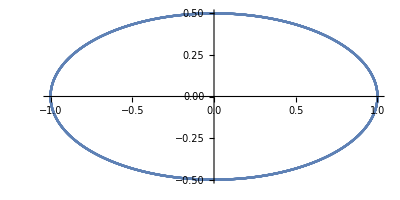

```mathematica
ParametricPlot[{k,e}/.tb4[[1;;8]],{xp,-π,π}]
```

```mathematica
ParametricPlot[{k,e}/.tb4[[9;;-1]],{θp,-π,π}]
```

-Graphics-

so an ellipse of TB points... weird? Is it genuine? Is that possible.

```mathematica
Clear[b,j,k]
es={
2e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
2e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.b->1/.j->-2k;
TableForm[es];

J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
det=Det[J]//FullSimplify;
tr=Tr[J]//FullSimplify;
temp=Flatten[{es,det,tr}];
tb5=Solve[temp==0]//FullSimplify;
Length[tb5]
```

552

```mathematica
tb5
```

{{e→-1/2,k→0,xm→ConditionalExpression[-π/2+2 π C[1], C[1]∈ℤ],xp→ConditionalExpression[2 π C[2], C[2]∈ℤ],θm→ConditionalExpression[-π/2+2 π C[3], C[3]∈ℤ],θp→ConditionalExpression[2 π C[4], C[4]∈ℤ]},{e→-1/2,k→0,xm→ConditionalExpression[-π/2+2 π C[1], C[1]∈ℤ],xp→ConditionalExpression[2 π C[2], C[2]∈ℤ],θm→ConditionalExpression[π/2+2 π C[3], C[3]∈ℤ],θp→ConditionalExpression[π+2 π C[4], C[4]∈ℤ]},548,{e→1/(2 √(2 ((2-3 ⅈ)+√(4-3 ⅈ)))),k→1/2 √(7+√(40+9 ⅈ)),xm→ConditionalExpression[ArcTan[Root0.308+0.181 ⅈRoot[1-4 #1+6 #1^2-4 #1^3+17 #1^4&,4]0.30839062865407557]+2 π C[1], C[1]∈ℤ],xp→ConditionalExpression[ArcTan[Root0.595+0.246 ⅈRoot[1-4 #1^2+8 #1^4-4 #1^6+#1^8&,6]0.5946035575013605]+2 π C[2], C[2]∈ℤ],θm→ConditionalExpression[π+ArcCot[Root-1.57+0.187 ⅈRoot[73-52 #1^2+14 #1^4-4 #1^6+#1^8&,2]-1.5650045718367604]+2 π C[3], C[3]∈ℤ],θp→ConditionalExpression[ArcTan[Root-1.44+0.595 ⅈRoot[1-4 #1^2+8 #1^4-4 #1^6+#1^8&,2]-1.435499972755075]+2 π C[4], C[4]∈ℤ]},{e→1/(2 √(2 ((2-3 ⅈ)+√(4-3 ⅈ)))),k→1/2 √(7+√(40+9 ⅈ)),xm→ConditionalExpression[ArcTan[Root0.308+0.181 ⅈRoot[1-4 #1+6 #1^2-4 #1^3+17 #1^4&,4]0.30839062865407557]+2 π C[1], C[1]∈ℤ],xp→ConditionalExpression[ArcTan[Root0.595+0.246 ⅈRoot[1-4 #1^2+8 #1^4-4 #1^6+#1^8&,6]0.5946035575013605]+2 π C[2], C[2]∈ℤ],θm→ConditionalExpression[ArcCot[√((1-2 ⅈ)+2 (-1)^(1/4))]+2 π C[3], C[3]∈ℤ],θp→ConditionalExpression[ArcTan[Root-1.44+0.595 ⅈRoot[1-4 #1^2+8 #1^4-4 #1^6+#1^8&,2]-1.435499972755075]+2 π C[4], C[4]∈ℤ]}}
 |  |  |  |

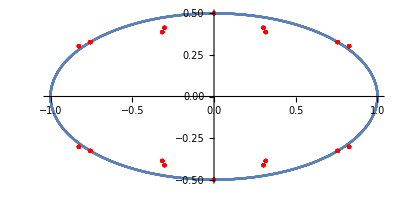

```mathematica
p1=ParametricPlot[{k,e}/.tb4[[1;;8]],{xp,-π,π}];
p2=ListPlot[{k,e}/.tb5,PlotStyle->{Red,PointSize[Large]}];
Show[{p1,p2}]
```

Huh. Something weird at J = -K...

### General J

```mathematica
Clear[b,j,k]
es={
2e-b Cos[xp] Sin[xm],
-b Sin[xp] Cos[xm]-j/2 Sin[2 xm]Cos[2 θm],
2e-b Cos[θp] Sin[θm],
-b Sin[θp] Cos[θm]-k/2 Sin[2 θm]Cos[2xm]
}/.b->1;
TableForm[es];

J={D[es, xp],D[es, xm],D[es, θp],D[es, θm]};
det=Det[J]//FullSimplify;
tr=Tr[J]//FullSimplify;
temp=Flatten[{es,det,tr}];
tb=Solve[temp==0];
Length[tb]
```

$Aborted

296

```mathematica
temp//TableForm
```

2 e-Cos[xp] Sin[xm]
-1/2 j Cos[2 θm] Sin[2 xm]-Cos[xm] Sin[xp]
2 e-Cos[θp] Sin[θm]
-1/2 k Cos[2 xm] Sin[2 θm]-Cos[θm] Sin[θp]
Sin[xm] Sin[xp] (j Cos[2 xm] Cos[2 θm]-Sin[xm] Sin[xp]) (Cos[θm]^2 Cos[θp]^2+Sin[θm] Sin[θp] (k Cos[2 xm] Cos[2 θm]-Sin[θm] Sin[θp]))+Cos[xm]^2 (-4 j k Sin[xm]^3 Sin[xp] Sin[θm] Sin[2 θm]^2 Sin[θp]+Cos[xp]^2 (Cos[θm]^2 Cos[θp]^2+Sin[θm] Sin[θp] (k Cos[2 xm] Cos[2 θm]-Sin[θm] Sin[θp])))
-((j+k) Cos[2 xm] Cos[2 θm])+2 (Sin[xm] Sin[xp]+Sin[θm] Sin[θp])